使用 MagneticTB 1.0 版

MagneticTB 2.0 也提供了 1.0 版函数。要继续使用 1.0 版 notebook，可以加载 MagneticTBOld`，调用名称末尾带 old 的函数。下面以石墨烯为例，介绍 1.0 版的初始化、Hamiltonian 和能带计算。

载入 MagneticTB 1.0 版

先启动一个新内核，用下面的命令加载 MagneticTBOld`。1.0 版与 2.0 版请分别在不同内核中使用：

```mathematica
Needs["MagneticTBOld`"]
```

用 1.0 版初始化模型

构造石墨烯模型时，给出六方晶格、一个碳原子的代表位置和 pz 轨道，对称操作会生成另一个碳原子。1.0 版的函数和选项名称末尾都带 old，完整输入如下：

```mathematica
grapheneOperationsOld = msgopold[grayold[191]];
initold[
  latticeold -> {
    {aold, 0, 0},
    {-aold/2, Sqrt[3] aold/2, 0},
    {0, 0, cold}
  },
  lattparold -> {aold -> 1, cold -> 3},
  wyckoffpositionold -> {
    {{1/3, 2/3, 0}, {0, 0, 0}}
  },
  symminformationold -> grapheneOperationsOld,
  basisFunctionsold -> {{"pz"}},
  debugQold -> False
];
```

用 1.0 版求出并显示 Hamiltonian

```mathematica
hOldOnsite = symhamold[1];
hOldNearest = symhamold[2];
hOld = hOldOnsite + hOldNearest;
MatrixForm[hOld]
```

(e1old | ⅇ^(ⅈ (-(2 kxold)/3-kyold/3)) t1old+ⅇ^(ⅈ (kxold/3-kyold/3)) t1old+ⅇ^(ⅈ (kxold/3+(2 kyold)/3)) t1old
ⅇ^(ⅈ (-kxold/3-(2 kyold)/3)) t1old+ⅇ^(ⅈ (-kxold/3+kyold/3)) t1old+ⅇ^(ⅈ ((2 kxold)/3+kyold/3)) t1old | e1old)

用 1.0 版画能带

```mathematica
oldPath = {
  {{{0, 0, 0}, {0, 1/2, 0}}, {"G", "M"}},
  {{{0, 1/2, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}}
};
bandManipulateold[oldPath, 30, hOld]
```

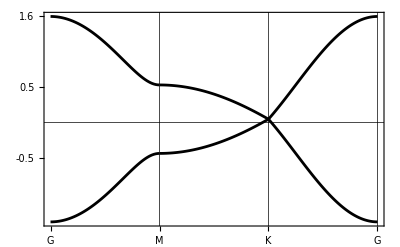

```mathematica
bandplotold[
  oldPath,
  60,
  hOld,
  {e1old -> 0.05, t1old -> 0.5}
]
```

比较 1.0 版与 2.0 版的结果

如果要比较 1.0 版与 2.0 版，在两个独立内核中输入相同的晶格、位置、对称操作和轨道，再比较得到的 Hamiltonian 和能带。两个版本都需要各自初始化，不会沿用另一个内核中的模型。

相关函数

initold ▪ symhamold ▪ bandManipulateold ▪ MagneticTB

历史